# Cálculo de las secciones transversales de absorción, esparcimiento y extinción

```mathematica
ConfigureMaTeX[
"pdfLaTeX"->"C:\\Users\\Poh\\AppData\\Local\\Programs\\MiKTeX\\miktex\\bin\\x64\\pdflatex.exe","Ghostscript"->"C:\\Program Files\\gs\\gs10.03.1\\bin\\gswin64c.exe"
]
```

{CacheSize→100,WorkingDirectory→Automatic,pdfLaTeX→C:\Users\Poh\AppData\Local\Programs\MiKTeX\miktex\bin\x64\pdflatex.exe,Ghostscript→C:\Program Files\gs\gs10.03.1\bin\gswin64c.exe}

```mathematica
Needs["MaTeX`"]
```

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
vlight=3*^17 ;(*nm s^-1*)
ϵ0=8.854187812*10^(-3)(*F/nm*);
```

Definiendo los factores de depolarización considerando los casos para un elipsoide oblato (a=b) L1= L2 y uno prolato (b=c) L2=L3

```mathematica
elipsoblato[a_,b_,c_]:=Module[{eac2=1-(c^2/a^2),gac=((1-(1-(c^2/a^2)))/(1-(c^2/a^2)))^(1/2),L1,L2,L3},
							L1=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2);
							L2=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2);
							L3=1-2 L1;
{L1,L2,L3}]
```

```mathematica
elipsprolato[a_,b_,c_]:=Module[{eab2=1-(b^2/a^2),L1,L2,L3},
							L1=((1-eab2)/eab2) (-1+((1/(2*Sqrt[eab2]))* Log[(1+Sqrt[eab2])/(1-Sqrt[eab2])]));
							L2=0.5*(1-L1);
							L3=0.5*(1-L1);{L1,L2,L3}];
```

```mathematica
factgeom[j_,a_,b_,c_]:=Which[a==b==c,1/3,a==b ,elipsoblato[a,b,c][[j]],
							b==c ,elipsprolato[a,b,c][[j]]]
```

```mathematica
factgeom[1,30.2,10,10]
```

0.107827

```mathematica
(*COMPROBANDO FUNCIONAMIENTO DE LOS FACTORES PARA OBLATO Y PROLATO*)
```

```mathematica
L1[a_,b_]:=Module[{eab2=1-(b^2/a^2),L1},L1=((1-eab2)/eab2) (-1+(1/(2*Sqrt[eab2])) Log[(1+Sqrt[eab2])/(1-Sqrt[eab2])])]
L11[a_,c_]:=Module[{eac2=1-(c^2/a^2),gac=((1-(1-(c^2/a^2)))/(1-(c^2/a^2)))^(1/2),L1},L1=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2)]
```

```mathematica
hola=Table[{Sqrt[1-(c^2/10^2)],L11[10,c]},{c,0.001,10,0.01}];
hola2=Table[{Sqrt[1-(b^2/10^2)],L1[10,b]},{b,0.001,10,0.01}];
```

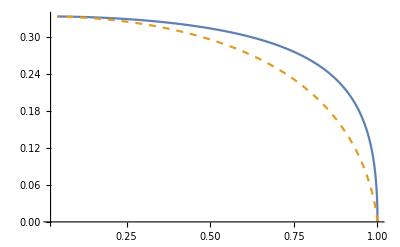

```mathematica
ListLinePlot[{hola,Style[hola2,Dashed]},PlotRange->All]
```

## Definiciones

### Función dieléctrica de tipo Drude

Definiendo la sección transversal de absorción

```mathematica
Cabs[a_,b_,c_,nm_,λ_,λp_,γ_]:=Module[{ϵp,ϵm,k,αx,αz,Cabs,Cabsx,Cabsz},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=1-((2 Pi vlight/λp)^2/((2 Pi vlight/λ)((2 Pi vlight/λ)+ I γ)));
										αx=4 π a b^2  ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵp-ϵm)));
										αz=4 π a b^2 ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵp-ϵm)));
										Cabs=k Im[2 αx+αz]/3;
										Cabsx=k Im[αx];
										Cabsz=k Im[αz];
										{Cabs,Cabsx,Cabsz}]
```

```mathematica
Csca[a_,b_,c_,nm_,λ_,λp_,γ_]:=Module[{ϵp,ϵm,k,αx,αz,Csca,Cscax,Cscaz},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=1-((2 Pi vlight/λp)^2/((2 Pi vlight/λ)((2 Pi vlight/λ)+ I γ)));
										αx=4 π a b^2  ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵp-ϵm)));
										αz=4 π a b^2 ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵp-ϵm)));
										Csca=k^4 Norm[2 αx+αz]^2/(18 Pi);
										Cscax=k^4 Norm[αx]^2/(6 Pi);
										Cscaz=k^4 Norm[αz]^2/(6 Pi);
										{Csca,Cscax,Cscaz}]
```

```mathematica
Cext[a_,b_,c_,nm_,λ_,λp_,γ_]:=Csca[a,b,c,nm,λ,λp,γ][[1]]+Cabs[a,b,c,nm,λ,λp,γ][[1]]
Cextx[a_,b_,c_,nm_,λ_,λp_,γ_]:=Csca[a,b,c,nm,λ,λp,γ][[2]]+Cabs[a,b,c,nm,λ,λp,γ][[2]]
Cextz[a_,b_,c_,nm_,λ_,λp_,γ_]:=Csca[a,b,c,nm,λ,λp,γ][[3]]+Cabs[a,b,c,nm,λ,λp,γ][[3]]
```

### Datos experimentales

```mathematica
Cabsexp[a_,b_,c_,nm_,λ_,np_]:=Module[{ϵp,ϵm,k,αx,αz,Cabs,Cabsx,Cabsz},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=np^2;
										αx=4 π a b^2  ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵp-ϵm)));
										αz=4 π a b^2 ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵp-ϵm)));
										Cabs=k Im[2αx+ αz]/3;
										Cabsx=k Im[αx];
										Cabsz=k Im[αz];
										{Cabs,Cabsx,Cabsz}]
```

```mathematica
Cscaexp[a_,b_,c_,nm_,λ_,np_]:=Module[{ϵp,ϵm,k,αx,αz,Csca,Cscax,Cscaz},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=np^2;
										αx=4 π a b^2  ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵp-ϵm)));
										αz=4 π a b^2 ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵp-ϵm)));
										Csca=k^4 (Norm[αz]^2+Norm[αx]^2+Norm[αx]^2)/(18 Pi);
										Cscax=k^4 Norm[αx]^2/(6 Pi);
										Cscaz=k^4 Norm[αz]^2/(6Pi);
										{Csca,Cscax,Cscaz}]
```

```mathematica
Cextexp[a_,b_,c_,nm_,λ_,np_]:=Cscaexp[a,b,c,nm,λ,np][[1]]+Cabsexp[a,b,c,nm,λ,np][[1]]
Cextexpx[a_,b_,c_,nm_,λ_,np_]:=Cscaexp[a,b,c,nm,λ,np][[2]]+Cabsexp[a,b,c,nm,λ,np][[2]]
Cextexpz[a_,b_,c_,nm_,λ_,np_]:=Cscaexp[a,b,c,nm,λ,np][[3]]+Cabsexp[a,b,c,nm,λ,np][[3]]
```

```mathematica
Cextexp[30,10,10,1.33,144,1]
```

66.7352

## Cálculos

### Datos experimentales

#### Aluminio

```mathematica
h vlight/0.5
```

2481.4

```mathematica
ϵ[w_,wp_,g_]:=1-((wp)^2/((w)((w)+ I * (g))))(*recibe en eV*)
```

```mathematica
alReal=Table[{ℏω,Re[ϵ[ℏω,13.142,0.197]]},{ℏω,3.5448580251428568,17,0.01}];
alImag=Table[{ℏω,Im[ϵ[ℏω,13.142,0.197]]},{ℏω,3.5448580251428568,17,0.01}];
```

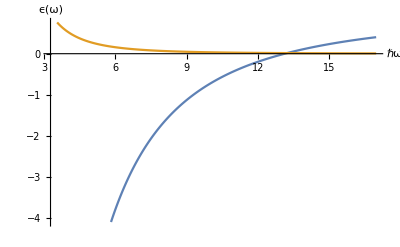

```mathematica
ListLinePlot[{alReal,alImag},AxesLabel->{"ℏω","ϵ(ω)"}]
```

Se graficará la Cext promedio contrastada con las Cext individuales

```mathematica
qextAlDrpromedio=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,135,300,0.07}];
```

```mathematica
upperTicksCext=Module[{labels,positions},labels={138,155,177,206,248,310};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];

upperTicksMinorCext=Module[{labels,positions,size},labels={3.5,4.2,4.6,6,8,9,12,40};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

#### Elipsoide oblato

#### Cambiando el tamaño de a

```mathematica
qextAlDr=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.05}];
qextAl1Dr=Table[{h vlight/λ,Cext[1.75,1.75,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.05}];
qextAl2Dr=Table[{h vlight/λ,Cext[2.0,2.0,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.01}];
qextAl3Dr=Table[{h vlight/λ,Cext[2.25,2.25,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.01}];
qextEsferaDr=Table[{h vlight/λ,Cext[2.0,2.0,2.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.01}];
```

```mathematica
upperTicksAl=Module[{labels,positions},labels={124,138,155,177,206,248,310};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorAl=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

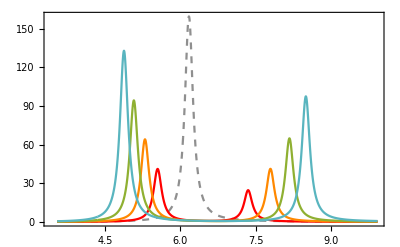

```mathematica
alc=ListLinePlot[{Style[qextEsferaDr,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAlDr,Red],Style[qextAl1Dr,RGBColor[1,0.533,0]],Style[qextAl2Dr,RGBColor[0.560181,0.691569,0.194885]],Style[qextAl3Dr,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],
FrameLabel->{{Style[MaTeX["C_{ext}\: [\mbox{nm}^2]"],Magnification->1.6],None},{Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinorAl,upperTicksAl]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.3]&/@{MaTeX["1"],MaTeX["1.5"],MaTeX["1.75"],MaTeX["2"],MaTeX["2.25"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLayout->{"Column",3},LegendLabel->Style[MaTeX["\mbox{AR}"],Magnification->1.3]],{0.73,0.75}]]
```

```mathematica
Export["Alc.svg",alc]
```

Alc.svg

#### Misma razón de aspecto

```mathematica
qextAlAR=Table[{h vlight/λ,Cext[1.0,1.0,0.5,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,400,0.01}];
qextAl1AR=Table[{h vlight/λ,Cext[1.5,1.5,0.75,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,400,0.01}];
qextAl2AR=Table[{h vlight/λ,Cext[2.0,2.0,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,400,0.01}];
qextAl3AR=Table[{h vlight/λ,Cext[2.5,2.5,1.25,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,400,0.01}];
qextAl3sphere=Table[{h vlight/λ,Cext[2.0,2.0,2.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,400,0.01}];
```

```mathematica
h vlight/3
```

413.567

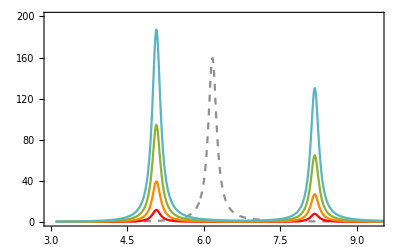

```mathematica
alAR=ListLinePlot[{Style[qextAl3sphere,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAlAR,Red],Style[qextAl1AR,RGBColor[1,0.533,0]],Style[qextAl2AR,RGBColor[0.560181,0.691569,0.194885]],Style[qextAl3AR,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],
FrameLabel->{{Style[MaTeX["C_{ext}\: [\mbox{nm}^2]"],Magnification->1.6],None},{Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinorAl,upperTicksAl]}},PlotRange->{{3,9.4},{0,200}},PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.3]&/@{MaTeX["2\mbox{ nm}"],MaTeX["1\mbox{ nm} "],MaTeX["1.5\mbox{ nm}"],MaTeX["2\mbox{ nm}"],MaTeX["2.5\mbox{ nm}"]}},LegendMarkerSize->{15,5},Spacings->{0.03},LegendLayout->{"Column",1},LegendLabel->Style[MaTeX["a"],Magnification->1.3]],{0.15,0.55}]]
```

```mathematica
Export["AlAR.svg",alAR]
```

AlAR.svg

#### Para ver las contribuciones cambiando a

```mathematica
qscaAlcontx=Table[{h vlight/λ,Csca[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ][[2]]},{λ,135,300,0.05}];
qscaAlcontz=Table[{h vlight/λ,Csca[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ][[3]]},{λ,135,300,0.05}];
qabsAlSphx=Table[{h vlight/λ,Cabs[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ][[2]]},{λ,135,300,0.05}];
qabsAlSphz=Table[{h vlight/λ,Cabs[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ][[3]]},{λ,135,300,0.05}];
```

```mathematica
qscaAlcont=Table[{h vlight/λ,Csca[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ][[1]]},{λ,135,300,0.05}];
qabsAlSph=Table[{h vlight/λ,Cabs[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ][[1]]},{λ,135,300,0.05}];
```

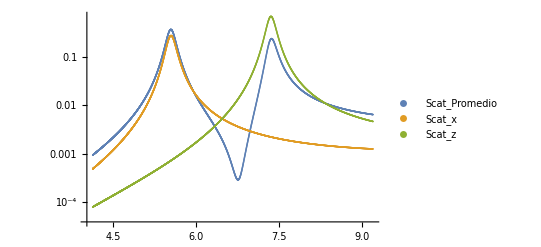

```mathematica
ListLogPlot[{qscaAlcont,qscaAlcontx,qscaAlcontz },PlotRange->All,PlotLegends->{"Scat_Promedio","Scat_x","Scat_z"}]
```

```mathematica
qabsAlcont=Table[{h vlight/λ,Cabs[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ][[1]]},{λ,135,300,0.05}];
qscaAlcont=Table[{h vlight/λ,Csca[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ][[1]]},{λ,135,300,0.05}];
qextAlcont=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,135,300,0.05}];
qabsAlSph=Table[{h vlight/λ,Cabs[1.5,1.5,1.5,1.33,λ,h vlight/(13.142),0.197/ℏ][[1]]},{λ,135,300,0.05}];
qscaAlSph=Table[{h vlight/λ,Csca[1.5,1.5,1.5,1.33,λ,h vlight/(13.142),0.197/ℏ][[1]]},{λ,135,300,0.05}];
```

```mathematica
h vlight/9
```

137.856

```mathematica
upperTicksAl=Module[{labels,positions},labels={138,155,177,206,248,310};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorAl=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

```mathematica
Export["AlContribuciones3.svg",alcont]
```

AlContribuciones3.svg